# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Little Tests

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=4;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: Same

```mathematica
(* Creating list of values for v0 *)
rangev0=Range[-10,0];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
(* See list of values for v0 *)
ListPlot[listv0];
```

```mathematica
row=20;
lvlmin=1;
lvlmax=3;

ic=ib;
pyrfiac=pyrfi[ia,ic,row,lvlmax];

e=0.05;
```

```mathematica
depthp=Table[
stereoDepth[listv0,ia,ic,lvlmax,{lvlmin,lvlmax},Range[p,p],Range[row,row],0.001,"ConstrainedNewMethod"]
,{p,1,30}][[All,1,1,3;;4]]
```

{{0.,0.},{0.,0.},{-3.99844,-1.17932},{-5.23459,-0.303212},{-4.25831,-1.27389},{-2.99338,-2.5736},{-1.97651,-3.59802},{-3.84239,-1.26793},{-6.12781,-0.852195},{-6.34663,-0.489354},{-4.75183,-2.13148},{-3.6996,-3.19267},{-3.16758,-3.66046},{-2.15884,-4.67249},{-1.37054,-5.4708},{-2.31005,-4.74042},{-2.46091,-4.4573},{-2.23531,-4.70788},{-5.53719,-1.23252},{-5.14605,-1.56971},{-3.83344,-2.9021},{-3.93536,-2.77483},{-4.79404,-1.77535},{-5.92292,-0.303766},{-5.01842,-1.21643},{-3.82236,-2.40064},{-2.8662,-3.35785},{-1.84751,-4.37551},{-0.682943,-5.54378},{-0.384556,-5.95491}}

```mathematica
pyrflowp=Table[
PyrFlow1D[10,p,listv0, pyrfiac[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),"ConstrainedNewMethod"][[1;;2]]
,{p,1,30}]
```

{{0.,0.},{0.,0.},{-3.99806,-1.17933},{-5.23463,-0.303212},{-4.25832,-1.27389},{-2.99891,-2.57359},{-1.97391,-3.59803},{-3.84691,-1.26794},{-6.12666,-0.852255},{-6.34165,-0.489585},{-4.75184,-2.13148},{-3.69959,-3.19267},{-3.16763,-3.66044},{-2.15606,-4.67244},{-1.36759,-5.47091},{-2.31005,-4.74042},{-2.46091,-4.4573},{-2.23531,-4.70788},{-5.55571,-1.18639},{-5.14752,-1.56959},{-3.82288,-2.90659},{-5.98843,-0.622186},{-4.24003,-2.50939},{-5.92189,-0.303772},{-5.02224,-1.21612},{-3.82215,-2.40064},{-2.86596,-3.35785},{-1.84734,-4.37552},{-0.682943,-5.54378},{-0.365506,-5.96152}}

```mathematica
iterp=Table[
PyrFlow1DIter[10,p,listv0, pyrfiac[[lvlmin;;lvlmax]],0.001*2^(-lvlmin+1),"ConstrainedNewMethod"][[-1,-1,1;;2]]
,{p,1,30}]
```

{{0.,0.},{0.,0.},{-3.99929,-1.17931},{-5.23464,-0.303212},{-4.2583,-1.27389},{-2.99727,-2.57358},{-1.97281,-3.59802},{-1.03529,-4.53357},{-1.79533,-3.57535},{-6.34375,-0.489517},{-4.75183,-2.13148},{-3.69959,-3.19267},{-3.16762,-3.66027},{-2.15755,-4.67225},{-1.36709,-5.47043},{-2.31005,-4.74042},{-2.46091,-4.4573},{-2.23531,-4.70788},{0.,0.},{-5.14646,-1.56953},{-3.82294,-2.9132},{-4.76654,-1.73955},{-18.0276,-1.76914},{-5.92256,-0.30377},{-5.01763,-1.21645},{-3.82226,-2.40064},{-2.86585,-3.35786},{-1.84764,-4.37551},{-0.682943,-5.54378},{-0.386011,-5.95406}}

#### Little Test: All packages

```mathematica
(* We move the image so intermediate cyclopean image haves bigger reach *)
dis=0;
ic=move[ib,dis]
steps=1;
```

-Graphics-

```mathematica
row=20;
lvlmin=1;
lvlmax=3;

pyrfiac=pyrfi[ia,ic,row,lvlmax];


e=0.05;
```

```mathematica
p0=46;
Plot[{pyrfiac[[lvlmin,1,1]][x],pyrfiac[[lvlmin,2,1]][x]},{x,1,103}];
```

```mathematica
(* Creating list of values for v0 *)
rangev0=Range[-10,0];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
(* See list of values for v0 *)
ListPlot[listv0];
```

```mathematica
seeAllLine[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],0.001,"ConstrainedNewMethod"];
```

```mathematica
ress=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],0.001,"ConstrainedNewMethod"];
```

```mathematica
res=Select[ress,#[[3]]=="converged"&];
```

```mathematica
Dimensions[res];
```

```mathematica
realp=res[[All,4]]-res[[All,1]];
```

```mathematica
index=DeleteDuplicates[Round[realp]];
(* Amount of cyclopean index capacity *)
Dimensions[index]
```

{39}

```mathematica
realPV=Flatten[{realp,-(Total[#]&/@res[[All,1;;2]])+dis},{{2},{1}}];
```

```mathematica
combinePV[realPV_]:=Block[{srtDistinctPV,newPV,i,c,sum,solution},(

srtDistinctPV=Sort[DeleteDuplicates[Round[realPV[[All,1]]]]];

newPV=SortBy[Flatten[{Round[realPV[[All,1]]],realPV[[All,2]]},{{2},{1}}],First];

i=1;

Table[
c=0;
sum=0;

While[newPV[[i,1]]==p, 
sum=newPV[[i,2]]+sum;
c=c+1;
i=i+1;
solution={p,sum/c}
];
solution

,{p,srtDistinctPV}]

)]
```

```mathematica
resPV=combinePV[realPV]
```

Part::partw: Part 97 of {{7,5.17809},{9,5.49384},{9,5.53219},{9,5.5378},{9,5.56367},{9,5.56712},{9,5.57141},{16,6.8295},{16,6.82979},{16,6.83583},«86»} does not exist.

{{7,5.17809},{9,5.54434},{16,6.85173},{18,7.05048},{19,6.91821},{20,6.94319},{25,6.72296},{27,6.74931},{28,6.60416},{30,6.24111},{34,5.74973},{35,5.45057},{40,5.52612},{41,5.44958},{43,5.32196},{46,5.29556},{50,5.33455},{51,5.40759},{52,5.37256},{57,5.24903},{58,2.65947},{64,9.81533},{67,9.79164},{68,9.68899},{71,9.61239},{73,9.41787},{74,9.59501},{75,7.02549},{76,5.32502},{79,5.33148},{80,5.31582},{85,5.61464},{89,5.2712},{94,5.29452},{95,5.30325},{100,5.2572},{101,5.22886},{102,5.21455},{104,2.22864}}

```mathematica
ListPlot[resPV[[All,1]]];
```

```mathematica
ListPlot[{ImageData[id][[row]],resPV},PlotLabels->{"Real","Rounded"},Joined->True,Mesh->All,PlotRange->{{1,110},{0,20}}]
```

-Graphics-

#### Little Test: Compare

```mathematica
combinePV[realPV_]:=Block[{srtDistinctPV,newPV,i,c,sum,solution},(

srtDistinctPV=Sort[DeleteDuplicates[Floor[realPV[[All,1]]+0.5]]];

newPV=SortBy[Flatten[{Floor[realPV[[All,1]]+0.5],realPV[[All,2]]},{{2},{1}}],First];

i=1;

Table[
c=0;
sum=0;

While[newPV[[i,1]]==p, 
sum=newPV[[i,2]]+sum;
c=c+1;
i=i+1;
solution={p,sum/c}
];
solution

,{p,srtDistinctPV}]

)]
```

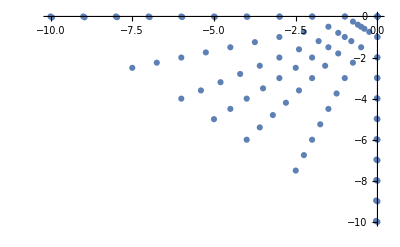

```mathematica
(* Creating list of values for v0 *)
rangev0=Range[-10,0];
r=Random[];
listv0=Join[{r,1-r}*#&/@rangev0,{1-r,r}*#&/@rangev0,{1,0}*#&/@rangev0,{0,1}*#&/@rangev0,{0.5,0.5}*#&/@rangev0,{0.25,0.75}*#&/@rangev0,{0.75,0.25}*#&/@rangev0,{0.4,0.6}*#&/@rangev0,{0.6,0.4}*#&/@rangev0];
(* See list of values for v0 *)
ListPlot[listv0]
```

```mathematica
(* Initial Values *)
dis=0;
ic=move[ib,dis];

row=30;
pyrfiac=pyrfi[ia,ic,row,lvlmax];

steps=0.2;

lvlmin=1;
lvlmax=4;

e=0.001;
```

```mathematica
(* Stereo Depth result *)
depth=stereoDepth[listv0,ia,ic,lvlmax,{lvlmin,lvlmax},Range[1,103,steps],Range[row,row],e,"ConstrainedNewMethod"][[1]];
Dimensions[depth]
```

{511,5}

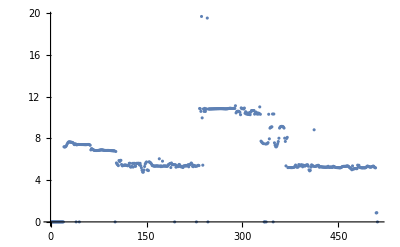

```mathematica
ListPlot[-depth[[All,1]]]
```

Part::partw: Part 473 of {{7,7.18605},{7,7.19376},{7,7.20126},«6»,{9,7.63167},«462»} does not exist.

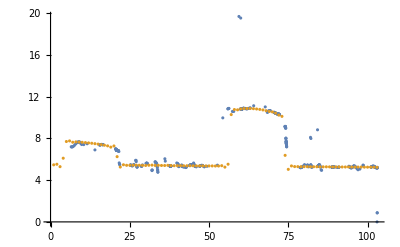

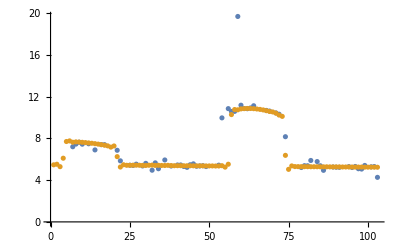

```mathematica
conDepth=Select[depth,#[[2]]=="converged"&];
posConDepth=Thread[{conDepth[[All,5]]-conDepth[[All,3]],-conDepth[[All,1]]+dis}];
posConDepth2=combinePV[posConDepth];
ListPlot[{posConDepth,ImageData[id][[row]]},PlotRange->All]
ListPlot[{posConDepth2,ImageData[id][[row]]},PlotRange->All]
```

```mathematica
(* line test result *)
ress=lineTest[listv0,Range[1,103,steps],pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"];
Dimensions[ress]
```

{511,4}

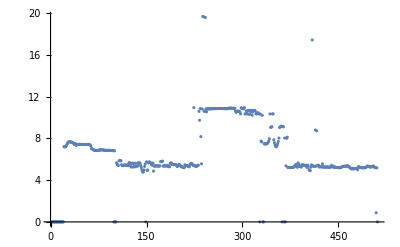

```mathematica
ListPlot[-Total[#]&/@ress[[All,1;;2]]]
```

Part::partw: Part 471 of {{7,7.18605},{7,7.19376},{7,7.20126},«6»,{9,7.63167},«460»} does not exist.

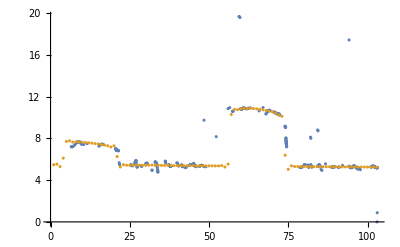

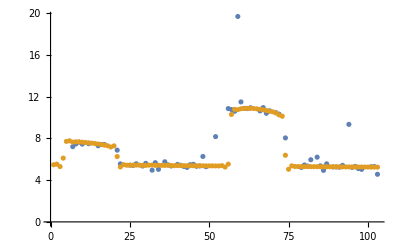

```mathematica
conRess=Select[ress,#[[3]]=="converged"&];
posConRess=Thread[{conRess[[All,4]]-conRess[[All,1]],-Total[#]&/@conRess[[All,1;;2]]+dis}];
posConRess2=combinePV[posConRess];
ListPlot[{posConRess,ImageData[id][[row]]},PlotRange->All]
ListPlot[{posConRess2,ImageData[id][[row]]},PlotRange->All]
```

#### Little Test: Errors

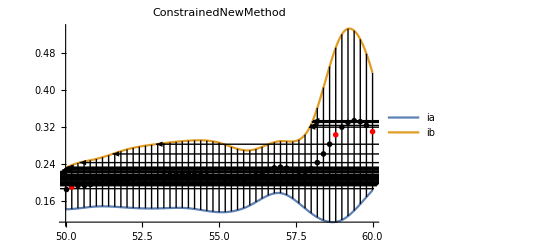

```mathematica
seeAllLine[listv0,Range[50,60,steps],pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

```mathematica
lineTest[listv0,Range[58,58,steps],pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

{{-2.84406,-8.04662,converged,58.}}

```mathematica
?pixelIterGraphics
```

```mathematica
ListAnimate[pixelIterGraphics[10,58,listv0,10,lvlmax,pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]]
```

```mathematica
PyrFlow1DIter[10,58,listv0,pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

{{{-5.51186,-5.20734,ok},{-5.89179,-5.06688,ok},{-5.89503,-5.06158,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged},{-5.89505,-5.06137,converged}},{{-6.0471,-3.65555,ok},{-5.53634,-6.30585,ok},{-5.52941,-5.92446,ok},{-5.52931,-5.85921,ok},{-5.52931,-5.84622,ok},{-5.52931,-5.84358,converged},{-5.52931,-5.84304,converged},{-5.52931,-5.84293,converged},{-5.52931,-5.84291,converged},{-5.52931,-5.8429,converged}},{{-4.04655,-6.8487,ok},{-4.02553,-6.74772,ok},{-4.01632,-6.71941,ok},{-4.01223,-6.71122,converged},{-4.0104,-6.70883,converged},{-4.00958,-6.70814,converged},{-4.00922,-6.70793,converged},{-4.00905,-6.70787,converged},{-4.00898,-6.70786,converged},{-4.00895,-6.70785,converged}},{{-3.89374,-7.9783,ok},{-3.00469,-8.00236,ok},{-2.93175,-8.01699,ok},{-2.89208,-8.02617,ok},{-2.87061,-8.03186,ok},{-2.85908,-8.03537,ok},{-2.8529,-8.03753,converged},{-2.8496,-8.03884,converged},{-2.84784,-8.03965,converged},{-2.8469,-8.04014,converged}}}

```mathematica
PyrFlow1D[10,58,listv0,pyrfiac[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"ConstrainedNewMethod"]
```

{-2.84548,-8.04107,converged}

#### Little Test: Full image

```mathematica
linemax=45;
```

```mathematica
(* Stereo Depth result *)
steps=1;
depth=stereoDepth[listv0,ia,ic,lvlmax,{lvlmin,lvlmax},Range[1,103,steps],Range[1,linemax],e,"ConstrainedNewMethod"];
Dimensions[depth]
```

{45,511,5}

```mathematica
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
,{r,linemax}];

Dimensions[resTable]
```

{45}

```mathematica
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,-resTable[[r,All,1]]}]
,{r,linemax}];

Dimensions[realPVTable]
realPVTable;
```

{45}

```mathematica
resPVTable=Table[
combinePV[realPVTable[[r]]]

,{r,linemax}];
Dimensions[resPVTable]
```

Part::partw: Part 473 of {{6,5.88958},{7,5.33901},{7,5.47498},{7,5.60441},{7,5.71242},{11,5.38387},{11,5.41642},{11,5.4195},{11,5.45941},{11,5.49255},«462»} does not exist.

Part::partw: Part 489 of {{1,0.},{4,2.47458},{7,5.40208},{7,5.40464},{7,5.40598},{7,5.4079},{7,5.40963},{7,5.40996},{7,5.41122},{7,5.41166},«478»} does not exist.

Part::partw: Part 479 of {{0,-1.02419},{0,-0.955173},{1,0.},{4,2.69264},{5,2.72916},{7,5.55313},{7,5.55492},{7,5.55554},{7,5.55912},{7,5.56102},«468»} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{45}

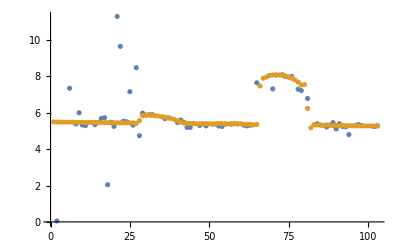

```mathematica
row=5;
ListPlot[{resPVTable[[row]],ImageData[id][[row]]},PlotRange->All]
```

```mathematica
createReplaceValues[resPVTable_]:=Block[{rows},(
rows=Length[resPVTable];
Flatten[Table[
Thread[Thread[{resPVTable[[r,All,1]],r}+0.5]->resPVTable[[r,All,2]]/max]
,{r,rows}],1]
)]
```

```mathematica
values=createReplaceValues[resPVTable];
```

```mathematica
im=Image[Table[0,{y,linemax},{x,103}]];
```

```mathematica
imm=ReplaceImageValue[im, values];
```

```mathematica
GraphicsRow[{ImageReflect[imm],id/max}]
```

-Graphics-